```mathematica
S[t_]:=Tanh[Log[1-t^2]]
```

```mathematica
Re[S[t]]
```

Re[(-1+(1-t^2)^2)/(1+(1-t^2)^2)]

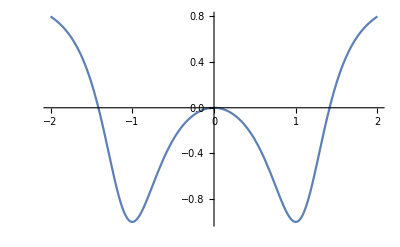

```mathematica
Plot[Re[S[t]],{t,-2,2}]
```

```mathematica
Solve[1/S[t]==0]
```

{{t→-√(1-ⅈ)},{t→√(1-ⅈ)},{t→-√(1+ⅈ)},{t→√(1+ⅈ)}}

```mathematica
Solve[S[t]==0]
```

{{t→0},{t→0},{t→-√2},{t→√2}}

```mathematica
Map[Simplify,Solve[S[t]==y,t]]
```

{{t→-√((-1+y-√(1-y^2))/(-1+y))},{t→√((-1+y-√(1-y^2))/(-1+y))},{t→-√((-1+y+√(1-y^2))/(-1+y))},{t→√((-1+y+√(1-y^2))/(-1+y))}}

```mathematica
->-√((-1+y+√(1-y^2))/(-1+y))},{t->√((-1+y+√(1-y^2))/(-1+y)),-√((-1+y+√(1-y^2))/(-1+y))}}
```

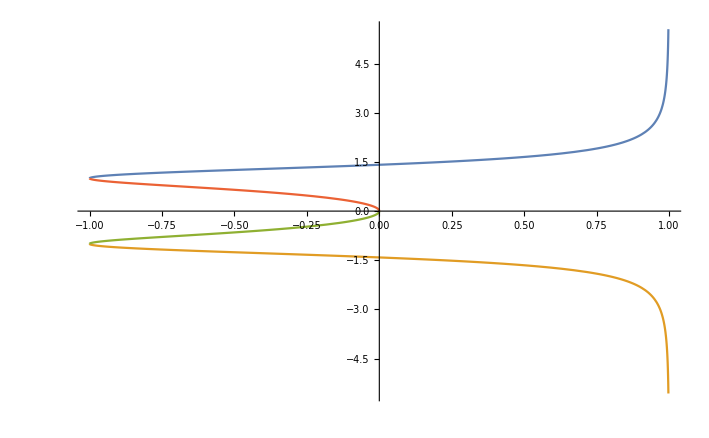

```mathematica
Plot[{√((-1+y-√(1-y^2))/(-1+y)),-√((-1+y-√(1-y^2))/(-1+y)),-√((-1+y+√(1-y^2))/(-1+y)),√((-1+y+√(1-y^2))/(-1+y))},{y,-1,1}]
```